```mathematica
$Assumptions = Im[F]==0&& Im[ν]==0;
```

```mathematica
h=1;
```

```mathematica
Eq1[ν_,F_,t_,a_]:=ⅈ h D[A[t],t] Exp[-ⅈ/h Integrate[-ν tt/2,{tt,a,t}]]-F B[t] Exp[-ⅈ/h Integrate[ν tt/2,{tt,a,t}]];
```

```mathematica
Eq2[ν_,F_,t_,a_]:=ⅈ h D[B[t],t] Exp[-ⅈ/h Integrate[ν tt/2,{tt,a,t}]]-F A[t] Exp[-ⅈ/h Integrate[-ν tt/2,{tt,a,t}]];
```

```mathematica
Sol[ν_,F_,a_,t0_,tf_,step_]:=NDSolve[{Eq1[ν,F,t,a]==0,Eq2[ν,F,t,a]==0,A[a]==0,B[a]==1},{A,B},{t,t0,tf},MaxStepSize->step,MaxSteps->Infinity];
```

```mathematica
A1[ν_,F_,a_,t0_,tf_,step_] :=(A[t]/.Sol[ ν,F,a,t0,tf,step])[[1]];
```

```mathematica
B1[ν_,F_,a_,t0_,tf_,step_] :=(B[t]/.Sol[ ν,F,a,t0,tf,step])[[1]];
```

```mathematica
Adata[ν_,F_,a_,t0_,tf_,step_,res_] := ($a=A1[ν,F,a,t0,tf,step];Table[$a,{t,t0,tf,res}]);
```

```mathematica
Bdata[ν_,F_,a_,t0_,tf_,step_,res_] := ($a=B1[ν,F,a,t0,tf,step];Table[$a,{t,t0,tf,res}]);
```

```mathematica
time[t0_,tf_,res_] := Table[t,{t,t0,tf,res}];
```

```mathematica
Aplot[ν_,F_,a_,t0_,tf_,step_,res_] :=
($a =Adata[ν,F,a,t0,tf,step,res]; ListLinePlot[Transpose[{time[t0,tf,res],$a*Conjugate[$a]}],PlotRange->All,AxesLabel->{"t","|B(t)|^2"}])
```

```mathematica
Bplot[ν_,F_,a_,t0_,tf_,step_,res_] :=
($a =Bdata[ν,F,a,t0,tf,step,res]; ListLinePlot[Transpose[{time[t0,tf,res],$a*Conjugate[$a]}],PlotRange->All,AxesLabel->{"t","|B(t)|^2"}])
```

```mathematica
ABplot[ν_,F_,a_,t0_,tf_,step_,res_] :=
($a =Adata[ν,F,a,t0,tf,step,res];
$b =Bdata[ν,F,a,t0,tf,step,res];  ListLinePlot[{Transpose[{time[t0,tf,res],$a*Conjugate[$a]}],Transpose[{time[t0,tf,res],$b*Conjugate[$b]}]}])
```

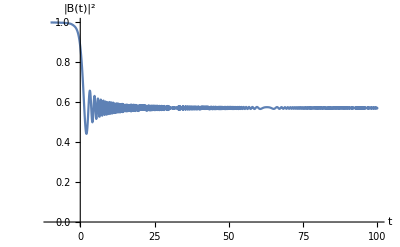

```mathematica
Bplot[1,.3,-100,-10,100,0.01,0.1]
```

```mathematica
B2[ν_, F_] := E^(-((2*Pi*F^2)/(h*ν)));
```

```mathematica
N[E^(-((2*Pi*.2^2)/(h*1))),20]
```

0.777768

```mathematica
Bdata[2,1,-100,-10,100,0.1,0.1][[Length[Bdata[2,1,-100,-10,100,0.1,0.1]-1]]]
```

1.+0. ⅈ

```mathematica
BBdata[ν_,F_,a_,t0_,tf_,step_,res_]:=($a =Bdata[ν,F,a,t0,tf,step,res]; Transpose[{time[t0,tf,res],Re[$a*Conjugate[$a]]}]);
```

```mathematica
Clear[Bdata]
```

```mathematica
af = Adata[1,.2,-100,-20,100,0.0001,0.001];
```

```mathematica
bf = Bdata[1,.2,-100,-1000,1000,0.0001,0.001];
```

```mathematica
ListLinePlot[{Transpose[{time[-20,100,0.001],af*Conjugate[af]}],Transpose[{time[-20,100,0.001],bf*Conjugate[bf]}]},AxesLabel->{t,"P_(a, b)"},PlotLegends->{"|A(t)|^2","|B(t)|^2"},PlotRange->All]
```

-Graphics-

```mathematica
bbb = Re[bf[[Length[bf]]]*Conjugate[ bf[[Length[bf]]]]]
```

0.779318

```mathematica
bbb2 = Re[bf[[Length[bf]]]*Conjugate[ bf[[Length[bf]]]]]
```

0.779318

```mathematica
(0.779318255838422-N[E^(-((2*Pi*.2^2)/(h*1))),20])/0.779318255838422
```

0.00198966